# Campos Eléctrico y Potencial en Mathematica #

Funciones que utilizaremos:

```mathematica
Modulo[r_,rq_]:=Sqrt[Power[r[[1]]-rq[[1]],2]+Power[r[[2]]-rq[[2]],2]];(*Funcion para obtener la distancia entre dos vectores*)
```

```mathematica
Ce[r_,rq_,q_:1]:=Times[rq-r ,Divide[q,4  π Power[Modulo[r,rq],3]]];(*Funcion para el campo electrico a partir del vector r, el posicion de particula y el vector orige ro*)
```

Variables para modificar los limites de gráfico y cuantas partículas:

```mathematica
lg=6;
np=8; (*lg,Limites del grafico,np = numero de particulas*)
ri:=RandomInteger[{- lg,lg}]
(*variable de valor diferido que funciona como funcion con un numero random de salida, ri es por Random Integer*)
rn:=RandomInteger[{1,4}];(*random natural; no se usa ri para no tener cargas iguales a 0*)
```

Correr la siguiente célula para obtener nuevas partículas:

```mathematica
PosR=Table[{ri,ri},{np}];(*genera una lista de posiciones aleatoras de tamano np*)
CarR=Table[RandomChoice[{1,-1}]*rn,{np}];  (*genera una lista de cargas aleatorias*)

CarI=Table[RandomChoice[{-1,1}] * 4,{np}];(*Lista de cargas identicas*)
BodyData={PosR,CarI}(*Datos de las particulas, con su pos. y car.*)
```

{{{-5,6},{3,2},{4,-4},{-1,6},{-4,3},{-3,-5},{6,1},{-5,5}},{-4,4,-4,-4,4,-4,4,-4}}

Este arrange de Funciones Suman los Campos Eléctricos

```mathematica
CampoE[x_,y_,BodyData_:BodyData]:=Table[Ce[{x,y},BodyData[[1]][[n]],BodyData[[2]][[n]]],{n,np}]
NetCampoEx[x_,y_,BodyData_:BodyData]:=Table[CampoE[x,y,BodyData][[n]][[1]],{n,np}]//Total
NetCampoEy[x_,y_,BodyData_:BodyData]:=Table[CampoE[x,y,BodyData][[n]][[2]],{n,np}]//Total
NetCampo[x_,y_,BodyData_:BodyData]:={NetCampoEx[x,y,BodyData],NetCampoEy[x,y]}
```

Gráfico del Campo Eléctrico

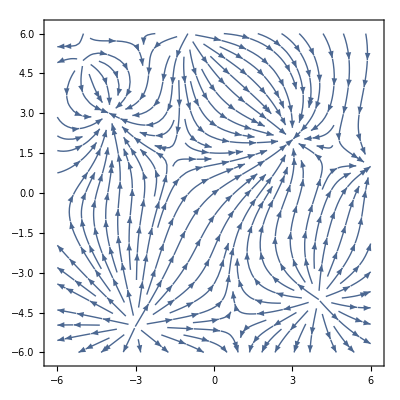

```mathematica
CampoElectricoG[BodyData_:BodyData,lg_:lg]:=StreamPlot[NetCampo[x,y,BodyData],{x,-lg,lg},{y,-lg,lg}]
CampoElectricoG[]
```

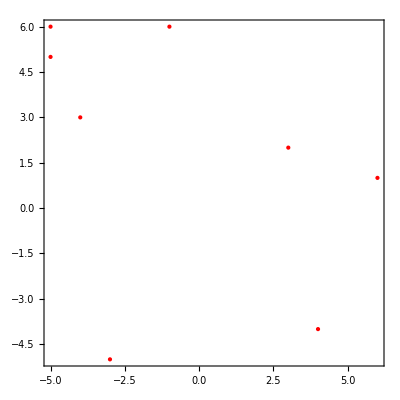

```mathematica
PuntosdeCarga=Graphics[Table[Style[Point[BodyData[[1]][[n]]],Red],{n,np}],Frame->True]
```

*Presento: El Campo Eléctrico*

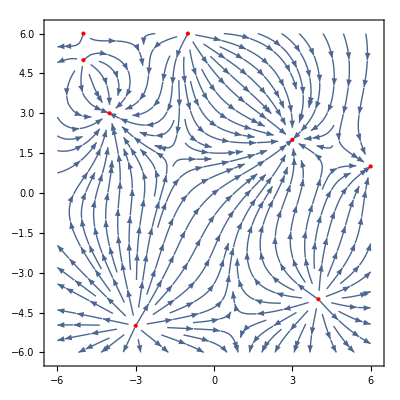

```mathematica
Show[CampoElectrico,PuntosdeCarga]
```

Potencial Eléctrico

```mathematica
PotE[r_,rq_,q_:1]:=Divide[q,4  π Modulo[r,rq]];(*Funcion para el Potencial electrico a partir del vector r*)
(*Funcion para Sumar los Potenciales*)
SPotencialE[x_,y_,BodyData_:BodyData]:=Table[PotE[{x,y},BodyData[[1]][[n]],BodyData[[2]][[n]]],{n,np}]//Total
```

```mathematica
PotencialElectricoG[BodyData_:BodyData,lg_:lg]:=Plot3D[SPotencialE[x,y,BodyData],{x,-lg,lg},{y,-lg,lg},ColorFunction->"SunsetColors",Mesh->None,PlotLegends->Automatic,PlotRange->{-2,2}]
PotencialElectricoG[]
```

-Graphics3D-

```mathematica
Particulas= Table[Style[Sphere[Append[BodyData[[1]][[n]],0],0.1],Red],{n,Lenght@BodyData[[2]]}];
Cargas=Table[Text[BodyData[[2]][[n]],Append[BodyData[[1]][[n]],.5]],{n,Lenght@BodyData[[2]]}];
PuntosdeCarga3D=Graphics3D[{Particulas[],Cargas[]}]
```

Table::iterb: Iterator {n,Lenght[{-4,-4,-4}]} does not have appropriate bounds.

-Graphics3D-

```mathematica
Show[PotencialElectrico,PuntosdeCarga3D,BoxRatios->Automatic,PlotRange->Automatic]
```

-Graphics3D-

Utilizando la Funcion Locator para Modificar la Posicion de las Particulas
Locator funciona

```mathematica
Locator[Dynamic[pos]] (*Efectua una actualizacion a las posiciones*)
```

```mathematica
Manipulate
```